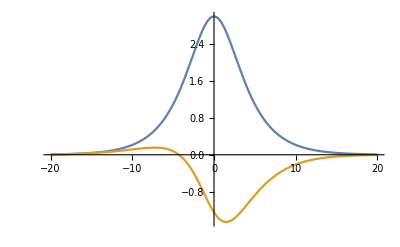

```mathematica
amp = 3;
width = 3;
phase = 2;
lin = 0.1;
chirp = 0;
f[x_] = amp/Cosh[x/width] Exp[I(phase+lin*x+chirp*x^2)];
Plot[{Abs[f[x]],Re[f[x]]},{x,-20,20},PlotRange->All]
```

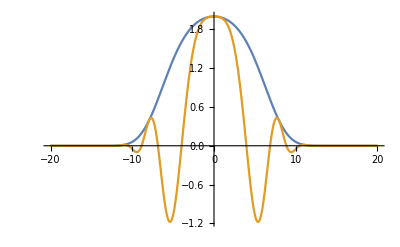

```mathematica
amp = 2;
width=10;
supwidth=1000;
chirp=0.1;
f[x_]=amp*Exp[-x^2/width^2-x^4/(4*supwidth)+I(chirp*x^2)];
Plot[{Abs[f[x]],Re[f[x]]},{x,-20,20},PlotRange->All]
```